```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True];
Clear[Np,Γ,τ];
yrotmatelem[k_,kp_]:=yrotmatelem[k,kp]=Sqrt[((k!)*((Np-k)!)*(kp!)*((Np-kp)!))]*Sum[(((-1.0)^n)*(Sqrt[1/2]^(k-kp+Np-2*n))*(Sqrt[1/2]^(2*n+kp-k)))/(((k-n)!)*((Np-kp-n)!)*(n!)*((kp-k+n)!)),{n,Max[k-kp,0],Min[k,Np-kp]}];
psi[τ_,k1_,k2_]=Sqrt[Binomial[Np,k1]*Binomial[Np,k2]]*(Cos[(k1-k2)*τ])^nc;
normfactor[τ_]:=Sum[Abs[psi[τ,k1,k2]]^2,{k1,0,Np},{k2,0,Np}];
psirot[τ_,k1_,k2_]:=Sum[psi[τ,k1px,k2px]*yrotmatelem[k1px,k1]*yrotmatelem[k2px,k2],{k1px,0,Np},{k2px,0,Np}];
ρB[τ_,k1_,k2_,k1p_,k2p_]:=psirot[τ,k1,k2]*Conjugate[psirot[τ,k1p,k2p]]/normfactor[τ];
ρBmatrix[τ_]:=ArrayFlatten[Table[ρB[τ,k1,k2,k1p,k2p],{k1,0,Np},{k1p,0,Np},{k2,0,Np},{k2p,0,Np}]];
ρC[τ_,k1_,k2_,k1p_,k2p_]:=ρB[τ,k1,k2,k1p,k2p]*Exp[-2*Γ*τ*((k1-k1p)^2+(k2-k2p)^2)];
ρCmatrix[τ_]:=ArrayFlatten[Table[ρC[τ,k1,k2,k1p,k2p],{k1,0,Np},{k1p,0,Np},{k2,0,Np},{k2p,0,Np}]];
ρDmatrix[τ_]:=ArrayFlatten[Table[ρC[τ,k1,k2p,k1p,k2],{k1,0,Np},{k1p,0,Np},{k2,0,Np},{k2p,0,Np}]];
lognegativity[τ_]:=Log[Np+1,Total[Abs[Eigenvalues[ρDmatrix[τ]]]]];
```

```mathematica
Np=2;θ=Pi/2;Γ=0;nc=Np;
τ=1.0;
lognegativity[τ]
```

0.786692

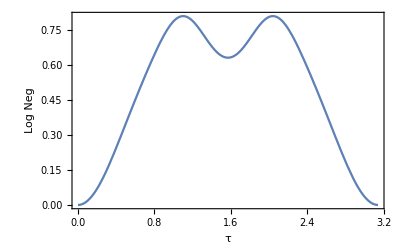

```mathematica
p1=Plot[lognegativity[τ],{τ,0,Pi},PlotRange->Automatic,FrameLabel->{"τ","Log Neg"}];
Print[p1];
```